# Synchronizing Metronomes (Entrainment)

## Analytic and Numerical Treatment

Ethan Knox

## Analytical Treatment

### Hanging Pendula on a Moving Platform

```mathematica
n:=2
vars:={q0[t],q1[t],q2[t]}
pvars2dvars:={q0'[t]->dq0[t],q1'[t]->dq1[t],q2'[t]->dq2[t]}
dvars2pvars:={dq0[t]->q0'[t],dq1[t]->q1'[t],dq2[t]->q2'[t]}
```

δw=w/(n-1)

```mathematica
dw:=w/(n-1)
```

x_i(t)=x_0(t)+(i-1) δw+l_i sin(q_i(t))
y_i(t)=-l_i cos(q_i(t))

```mathematica
x1[t_]:=q0[t]+l1 Sin[q1[t]]
y1[t_]:=-l1 Cos[q1[t]]
x2[t_]:=q0[t]+dw+l2 Sin[q2[t]]
y2[t_]:=-l2 Cos[q2[t]]
```

v_i(t)=√(((ẋ)_i)^2+((ẏ)_i)^2)→ v_i^2=((ẋ)_i)^2+((ẏ)_i)^2

```mathematica
v21[t_]:=(x1'[t])^2+(y1'[t])^2
v22[t_]:=(x2'[t])^2+(y2'[t])^2
```

T=1/2 M((ẋ)_0)^2+(∑^n)_(i=1)1/2 m_i(v_i^2+α_i l_i^2((q̇)_i)^2)
V=(∑^n)_(i=1)m_i gy_i

```mathematica
T[t_]:=M/2 (q0'[t])^2+m1/2 (v21[t]+α1 l1^2 (q1'[t])^2)+m2/2 (v22[t]+α2 l2^2 (q2'[t])^2)
V[t_]:=m1 g y1[t]+m2 g y2[t]
```

L=T-V

```mathematica
L[t_]:=T[t]-V[t]
Ld[t_]:=L[t]/.pvars2dvars
Lp[t_]:=L[t]/.dvars2pvars
```

```mathematica
Φ[t_]:=1/2 (k0 q0'[t]+k1 (x1'[t]^2+y1'[t]^2)+k2 (x2'[t]^2+y2'[t]^2))
Q0[t_]:=-D[Φ[t]/.pvars2dvars,dq0[t]]
Q1[t_]:=-D[Φ[t]/.pvars2dvars,dq1[t]]
Q2[t_]:=-D[Φ[t]/.pvars2dvars,dq2[t]]
EL0:=D[D[Ld[t],dq0[t]]/.dvars2pvars,t]-D[Lp[t],q0[t]]==Q0[t]
EL1:=D[D[Ld[t],dq1[t]]/.dvars2pvars,t]-D[Lp[t],q1[t]]==Q1[t]
EL2:=D[D[Ld[t],dq2[t]]/.dvars2pvars,t]-D[Lp[t],q2[t]]==Q2[t]
ode:=FullSimplify[{EL0,EL1,EL2}/.dvars2pvars]
ics={q1'[0]==0,q2'[0]==0,q0'[0]==0,q1[0]==q10,q2[0]==q20,q0[0]==0};
```

## Numerical Treatment

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
α1=1/3;α2=1/3;
l1=1;l2=1;
m1=1;m2=1;
M=1;k0=0.10;
k1=0.0;k2=0.0;
w=1;
g=1+0 9.81;
q10=0 π/8+π/16;q20=0 π/8;
time=100000;
```

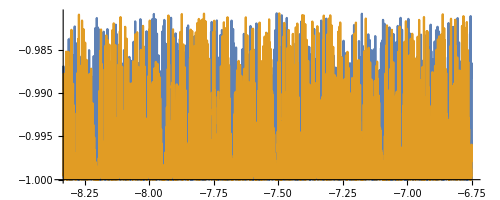

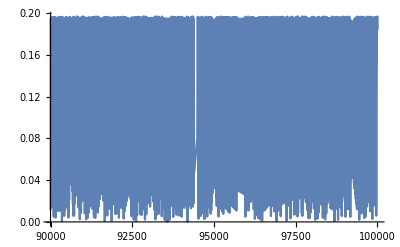

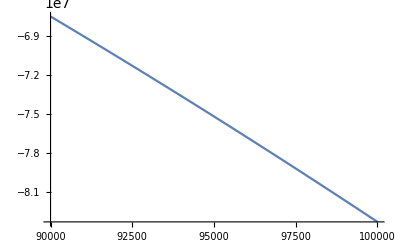

```mathematica
sol=First[NDSolve[Flatten[{ode,ics}],vars,{t,0,time}]];
x0[t_]:=Evaluate[q0[t]/.sol]
x1[t_]:=Evaluate[(q0[t]+Sin[q1[t]])/.sol]
x2[t_]:=Evaluate[(q0[t]+dw+Sin[q2[t]])/.sol]
y1[t_]:=Evaluate[-Cos[q1[t]]/.sol]
y2[t_]:=Evaluate[-Cos[q2[t]]/.sol]

ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]}},{t,0.9 time,time}]
Plot[(Abs[q1[t]-q2[t]])/.sol,{t,0.9 time,time}]
Plot[q0[t]/.sol,{t,0.9 time,time}]

(*min=-2
max=2
frames=Table[Graphics[{Gray,Thick,Line[{{x0[t],0},{x1[t],y1[t]}}],Line[{{x0[t]+1,0},{x2[t],y2[t]}}],Darker[Red],Rectangle[{x0[t],0},{x0[t]+w,0.25}],Darker[Blue],Disk[{x1[t],y1[t]},.1],Disk[{x2[t],y2[t]},.1]},PlotRange->{{min,max},{-2.5,2.5}}],{t,0,time,.1}];
ListAnimate[frames,AnimationRunning->False]
Export["C:/users/ethan/documents/code/test.avi",%]*)
Quit[]
```

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}